0.567143

-2.55493×10^-10

7.94316×10^-10

39

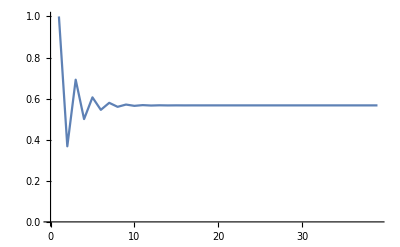

```mathematica
f[x_]=ⅇ^-x-x;
g[x_]=f[x]+x;
Emin=10^-9;
Nmax=1000;
Iteraciones=0;
dh=0.001;
Bandera=0;
Error=1;
Datos={};

While[(Bandera==0&&Error≠0&&Iteraciones<10),
Xi=Input["Introduce Xi"];
Der=(g[Xi+dh]-g[Xi])/dh;
If[Abs[Der]≤1,Bandera=1,Bandera=0];
If[f[Xi]==0,Error=0,Error=1];
Iteraciones++
	]
Iteraciones=0;
While[(Error≥ Emin&&Iteraciones≤ Nmax&&Bandera==1),
Xact=g[Xi];
AppendTo[Datos,Xact];
If[Xact==0,Xact=Emin, Xact=Xact];
Error=Abs[(Xact-Xi)/Xact];
If[f[Xact]==0,Error=0,Error=Error];
Xi=Xact;
Iteraciones++
]

Xact//N
f[Xact]//N
Error//N
Iteraciones
ListPlot[Datos,Joined->True,PlotRange->All]
```